```mathematica
GenerateGradientsGUI[]
```

# QMRITools Demonstration

In this demo notebook some functionality of the QMRI toolbox is demonstrated.
Not all functionality is covered, some functions are very specialized for experiments only run in our lab. 
Furthermore some functionality is still under development and therefore will also be excluded from the demos.

Initialization

Load the toolbox and specify the directory of the demo data folder. It assumes the demo data folder is in the same folder as the demo.nb

```mathematica
<<QMRITools`
SetDirectory[FileNameJoin[{NotebookDirectory[],"DemoData"}]];
```

```mathematica
pack=Last[PacletFind["QMRITools"]]
Information@pack
```

PacletObject[…]

Paclet

### List all Packages and toolboxes

List of all the QMRITool packages and functions that are loaded. For more information about the functions open the “All-Functions.nb”

```mathematica
NotebookOpen@FileNameJoin[Append["Location"/.PacletInformation[PacletFind["QMRITools"]],"All-Functions.nb"]];
```

```mathematica
Column@QMRIToolsPackages[]
```

CardiacTools
CoilTools
DenoiseTools
DixonTools
ElastixTools
GeneralTools
GradientTools
ImportTools
IVIMTools
JcouplingTools
MaskingTools
NiftiTools
PhysiologyTools
PlottingTools
ProcessingTools
RelaxometryTools
SimulationTools
TensorTools
VisteTools

```mathematica
QMRIToolsFunctions[25]
```

Functions

ADCCalc | CentralAxes | DatWrite | ExportBval | GetPulseProfile | ImportNii | MakeWeightMask | PCAFitHist | RadialSample | SaveImage | SNRCalc | UnwrapSplit
AddNoise | ClearTemporaryVariables | DcmToNii | ExportBvec | GetSliceData | ImportNiiDiff | Mask | PhaseAlign | ReadBrukerDiff | SegmentMask | SNRMapCalc | VectorToData
AlignRespLog | CoilSNRCalc | DeNoise | ExportNii | GetSliceNormal | ImportNiiDix | MaskData | PlotContour | ReadBvalue | SequencePulseAcquire | SortDiffusionData | WeightMapCalc
AngleCalc | ColorFAPlot | Deriv | ExportVol | GetSliceNormalDir | ImportNiiT1 | MaskHelix | PlotCorrection | ReadDicom | SequenceSpinEcho | SplitSegmentations | 
AngleMap | CompilebleFunctions | DevideNoZero | ExtractNiiFiles | GetSlicePositions | ImportNiiT2 | MeanNoZero | PlotData | ReadDicomDiff | SequenceSteam | SplitSets | 
AnisoFilterTensor | CompressNiiFiles | DictionaryMinSearch | FACalc | GetSpinSystem | ImportPhyslog | MeanRange | PlotData3D | ReadDicomDir | SequenceTSE | StdFilter | 
ApplyCrop | ConcatenateDiffusionData | DixonReconstruct | FConvert | GfactorSimulation | ImportRespirect | MeanSignal | PlotDefGrid | ReadDicomDirDiff | SetupDataStructure | StichData | 
AutoCropData | ConditionNumberCalc | DixonToPercent | FConverti | GradBmatrix | ImportVol | MeanStd | PlotDuty | ReadGradients | ShiftPar | SumOfSquares | 
BayesianIVIMFit2 | ConvertGrads | DriftCorrect | FiberDensityMap | GradientPlot | InvertDataset | MedCouple | PlotIVIM | ReadTransformParameters | ShiftPulseProfile | SysTable | 
BayesianIVIMFit3 | Correct | DTItoolExp | FiberLengths | GradRead | IVIMCalc | MedianNoZero | PlotMoments | ReadVoxSize | SigmaCalc | T1Fit | 
BlochSeries | CorrectBmatrix | DTItoolExpFile | FileSelect | GradSeq | IVIMCorrectData | MemoryUsage | PlotPhyslog | RegisterCardiacData | Signal | T1rhoFit | 
Bmatrix | CorrectGradients | DTItoolExpInd | FinalGrads | GridData | IVIMFunction | MergeSegmentations | PlotRespiract | RegisterData | SimAddPhase | T2Fit | 
BmatrixCalc | CorrectJoinSetMotion | DTItoolExpTens | FindCoilPosition | GridData3D | IVIMResiduals | NNLeastSquares | PlotSegmentMask | RegisterDataSplit | SimAngleParameters | TensMat | 
BmatrixConv | CorrectParMap | ECalc | FindCrop | HelixAngleCalc | JoinSets | NoiseCorrelation | PlotSegments | RegisterDataTransform | SimEvolve | Tensor | 
BmatrixInv | CreateDiffData | ECVCalc | FindMaxDimensions | Hist | LapFilter | NoiseCovariance | PlotSequence | RegisterDataTransformSplit | SimHamiltonian | TensorCalc | 
BmatrixRot | CreateHeart | EigensysCalc | FindOrder | Hist2 | ListSpherePlot | NonLinearEPGFit | PlotSimulation | RegisterDiffusionData | SimParameters | TensorCorrect | 
BmatrixToggle | CreateT2Dictionary | EigenvalCalc | FindOutliers | HistogramPar | LoadCoilSetup | NormalizeData | PlotSimulationAngle | RegisterDiffusionDataSplit | SimReadout | TensVec | 
BullseyePlot | CropData | EigenvecCalc | FitData | HomoginizeData | LoadCoilTarget | NumberTableForm | PlotSimulationAngleHist | RemoveIsoImages | SimRotate | ThetaConv | 
BvalRead | CutData | EnergyCalc | FracCorrect | ImportBmat | LoadFiberTracts | OverPlusCalc | PlotSimulationHist | RemoveMaskOverlaps | SimSignal | ThetaConvi | 
CalculateGfactor | Data2DToVector | EPGSignal | FullGrad | ImportBval | LogNoZero | PadToDimensions | PlotSimulationVec | RescaleData | SimSpoil | TransData | 
CalculateMoments | Data3DToVector | EPGT2Fit | GenerateGradients | ImportBvalvec | MADNoZero | ParameterCalc | PlotSpectrum | RescaleSegmentation | SimulateDixonSignal | TransformData | 
CalculateWallMap | DataTransformation | ErrorPlot | GenerateGradientsGUI | ImportBvec | MakeCoilLayout | ParameterFit | Pulses | ResidualCalc | SimulateSliceEPG | TransmuralPlot | 
CalibrateEPGT2Fit | DatRead | ExcludeSlices | GetGradientScanOrder | ImportDTI | MakeECVBloodMask | ParameterFit2 | QMRIToolsFuncPrint | ReverseCrop | SmartMask | TriExponentialT2Fit | 
CardiacCoordinateSystem | DatTot | ExpNoZero | GetMaskData | ImportExploreDTItens | MakeNoisePlots | PCADeNoise | QMRIToolsFunctions | RMSNoZero | SmoothMask | UniqueBvalPosition | 
CardiacSegment | DatTotXLS | ExportBmat | GetMaskMeans | ImportGradObj | MakeSliceImages | PCAFitEq | QMRIToolsPackages | ROIMask | SmoothSegmentation | Unwrap |

Options

AffineDirections | ConvertDcm | DixonPrecessions | FixPseudoDiffSD | Iterations | Method | OutlierIterations | PCAWeighting | ReportFits | SpectrumColor | UseMask
AnisoFilterSteps | CorrectPar | DixonTollerance | FlipAxes | IterationsA | Method | OutlierMethod | PeakNumber | Resolutions | SphereColor | UseMask
AnisoKappa | CropInit | DropSamples | FlipBvec | IVIMComponents | Method | OutlierOutput | PhaseEncoding | ResolutionsA | SphereSize | VisualOpt
AnisoStepTime | CropOutput | DropSlices | FlipGrad | IVIMConstrained | Method | OutlierRange | PlotColor | ReverseData | SplitMethod | WaterFatShift
AnisoWeightType | CropPadding | EPGCalibrate | FullOutput | IVIMConstrains | Method | OutputCalibration | PlotLabel | ReverseSets | StartPoints | WaterFatShiftDirection
AxesLabel | CutOffMethod | EPGFatShift | FullSphere | IVIMFixed | Method | OutputCheckImage | PlotLabel | RobustFit | StartSlices | WindowTitle
AxesMethod | DeleteTempDirectory | EPGFitFat | GetMaskOutput | IVIMTensFit | MethodReg | OutputCoilSurface | PlotRange | RobustFitParameters | Steps | 
BackgroundValue | DeNoiseIterations | EPGFitPoints | GOutput | JoinSetSplit | MethodReg | OutputImage | PlotRange | RotateGradient | StepSizeI | 
BinaryType | DeNoiseKernel | EPGMethod | GradType | LineStep | MethodRegA | OutputMethod | PlotRange | RotateGradients | Strictness | 
BloodMaskRange | DeNoiseMonitor | EPGMethodCal | GRegularization | LineThreshold | MonitorCalc | OutputPlot | PlotRange | RotationCorrect | SwitchAxes | 
BmatrixOut | DictB1Range | EPGRelaxPars | GridLineSpacing | Linewidth | MonitorEPGFit | OutputSamples | PlotRange | RowSize | TableAlignments | 
BsplineDirections | DictT2fRange | EPGSmoothB1 | HelixMethod | LinewidthShape | MonitorIVIMCalc | OutputSNR | PlotSolution | Runs | TableDepth | 
BsplineSpacing | DictT2fValue | FatFieldStrength | HistogramBins | MagnetizationVector | MonitorUnwrap | OutputTransformation | PlotSpace | SampleStep | TableDirections | 
BullPlotMethod | DictT2IncludeWater | FieldStrength | HistogramBinsA | MakeCheckPlot | MotionCorrectSets | OutputType | PlotStyle | ScaleCorrect | TableHeadings | 
CenterFrequency | DictT2Range | FileType | ImageLegend | MaskClosing | NiiDataType | OutputWeights | PositiveZ | Scaling | TableMethod | 
ChainSteps | DistanceMeasure | FilterMaps | ImageResolution | MaskCompartment | NiiMethod | PadDirection | PrintTempDirectory | SeedDensity | TableSpacing | 
CoilArrayPlot | Distribution | FilterShape | ImageSize | MaskComponents | NiiScaling | PaddOverlap | RadialSamples | ShowFit | TempDirectory | 
CoilSurfaceVoxelSize | DixonAmplitudes | FilterSize | ImageSize | MaskFiltKernel | NoiseSize | PadValue | ReadoutBandwith | ShowHelixPlot | TensOutput | 
ColorFunction | DixonFieldStrength | FilterType | ImageSize | MaskSmoothing | NormalizeIVIM | Parallelize | ReadoutOutput | SliceRange | TextOffset | 
ColorFunction | DixonFilterInput | FindTransform | ImageSize | MaskWallMap | NormalizeSets | Parallelize | ReadoutPhase | SliceRangeSamples | TextSize | 
ColorFunction | DixonFilterOutput | FitConstrains | ImageSize | MeanMethod | NormalizeSignal | PCAComponents | ReadoutSamples | SmartMaskOutput | UnitMulti | 
ColorValue | DixonFilterSize | FitFunction | InterpolationOrder | MeanRes | NumberSamples | PCAFitParameters | RegistrationTarget | SmartMethod | UnwrapDimension | 
CompressNii | DixonFrequencies | FitOutput | InterpolationOrder | Method | NumberSamplesA | PCAKernel | Reject | SmoothHelix | UpdateStep | 
ConditionCalc | DixonIterations | FitSigma | InterpolationOrderReg | Method | OrderSpan | PCAOutput | Reject | SmoothSNR | UseGPU | 
ContourStyle | DixonMaskThreshhold | FixPseudoDiff | InterpolationOrderRegA | Method | OutlierIncludeZero | PCATollerance | RejectMap | SortVecs | UseGrad |

```mathematica
CompilebleFunctions[]
```

Abs | Decrement | Last | Quotient | TimesBy
AddTo | Delete | Length | Ramp | Tr
And | DeleteCases | Less | Random | Transpose
Append | Dimensions | LessEqual | RandomChoice | Unequal
AppendTo | Divide | List | RandomComplex | Union
Apply | DivideBy | Log | RandomInteger | Unitize
ArcCos | Do | Log10 | RandomReal | UnitStep
ArcCosh | Dot | Internal`Log1p | RandomSample | UnsameQ
ArcCot | Drop | Log2 | RandomVariate | VectorQ
ArcCoth | Equal | LogGamma | Range | Which
ArcCsc | Erf | LogisticSigmoid | Re | While
ArcCsch | Erfc | LucasL | RealAbs | With
ArcSec | EvenQ | Map | RealSign | Xor
ArcSech | Exp | MapAll | Internal`ReciprocalSqrt | 
ArcSin | Internal`Expm1 | MapAt | ReplacePart | 
ArcSinh | Fibonacci | MapIndexed | Rest | 
ArcTan | First | MapThread | Return | 
ArcTanh | FixedPoint | NDSolve`FEM`MapThreadDot | Reverse | 
Arg | FixedPointList | MatrixQ | RotateLeft | 
Array | Flatten | Max | RotateRight | 
ArrayDepth | NDSolve`FEM`FlattenAll | MemberQ | Round | 
Internal`Bag | Floor | Min | RuleCondition | 
Internal`BagPart | Fold | Minus | SameQ | 
BitAnd | FoldList | Mod | Scan | 
BitNot | For | Compile`Mod1 | Sec | 
BitOr | FractionalPart | Module | Sech | 
BitXor | FreeQ | Most | SeedRandom | 
Block | Gamma | N | Select | 
BlockRandom | Compile`GetElement | Negative | Set | 
Boole | Goto | Nest | SetDelayed | 
Break | Greater | NestList | Compile`SetIterate | 
Cases | GreaterEqual | NonNegative | Sign | 
Catch | Gudermannian | Not | Sin | 
Ceiling | Haversine | OddQ | Sinc | 
Chop | If | Or | Sinh | 
Internal`CompileError | Im | OrderedQ | Sort | 
System`Private`CompileSymbol | Implies | Out | Sqrt | 
Complement | Increment | Outer | Internal`Square | 
ComposeList | Indexed | Part | Internal`StuffBag | 
CompoundExpression | Inequality | Partition | Subtract | 
Conjugate | Compile`InnerDo | Piecewise | SubtractFrom | 
ConjugateTranspose | Insert | Plus | Sum | 
Continue | IntegerDigits | Position | Switch | 
Cos | IntegerPart | Positive | Table | 
Cosh | Intersection | Power | Take | 
Cot | InverseGudermannian | PreDecrement | Tan | 
Coth | InverseHaversine | PreIncrement | Tanh | 
Count | Compile`IteratorCount | Prepend | TensorRank | 
Csc | Join | PrependTo | Throw | 
Csch | Label | Product | Times |

### Memory Usage

```mathematica
MemoryUsage[]
```

MemoryUsage gives a visual overview of all datasets in memory

Basic Data manipulation and visualisation

### Import and show Data

```mathematica
(*simple 3D dataset*)
{data,vox}=ImportNii["twoLegs.nii"];
```

```mathematica
(*plot the data*)
PlotData[data,vox]
```

```mathematica
(*plot the data as a grid*)
PlotData[GridData[data,5]]
```

```mathematica
(*plot every third slice of the the data as a grid*)
PlotData[GridData[data[[;;;;3]],3]]
```

```mathematica
(*plot every third slice of the the data as a grid, with auto cropping*)
PlotData[GridData[First[AutoCropData[data]][[1;;;;3]],3]]
```

```mathematica
(*3D data viewer, Still work in progress*)
PlotData3D[AutoCropData[data][[1]],vox]
```

All Nii files in a folders can be compressed or uncompressed using "CompressNiiFiles" and "ExtractNiiFiles".
The nii import function is blind to the .gz extension.  
To convert Dcm to nii format used DcmToNii

```mathematica
CompressNiiFiles[]
```

```mathematica
ExtractNiiFiles[]
```

```mathematica
DcmToNii[]
```

### Automatically find cross section images

By also providing the voxel size the pos is in mm else it will be in vox position

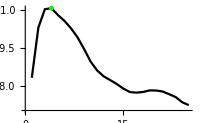
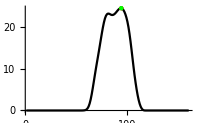
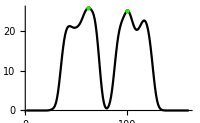

```mathematica
pos=GetSlicePositions[data,MakeCheckPlot->True];
pdat=GetSliceData[data,pos];
```

```mathematica
Grid[MakeSliceImages[pdat,vox,ColorFunction->"GrayTones"]]
```

```mathematica
Grid[MakeSliceImages[pdat,vox,ColorFunction->"DarkRainbow",ImageLegend->True]]
```

### Rescaling Data

```mathematica
(*to specific dimensions*)
dataReD=RescaleData[data,{50,100,100}];

Dimensions[data]
Dimensions[dataReD]
```

{25,160,160}

{50,100,100}

```mathematica
(*to specific voxel Size*)
voxNew={4,2,2};
dataRe=RescaleData[data,{vox,voxNew}];

Dimensions[data]
Dimensions[dataRe]
```

{25,160,160}

{38,240,240}

### Cropping

#### Automatic crop

```mathematica
(*Find corp finds the crop values to remove zero background*)
crop=FindCrop[data];
```

```mathematica
(*apply thecropping*)
dataCrop=ApplyCrop[data,crop];
```

```mathematica
PlotData[dataCrop,vox]
```

```mathematica
(*do this in one go*)
{dataCrop,crop}=AutoCropData[data];
```

```mathematica
PlotData[dataCrop,vox]
```

#### Apply To Rescaled Data

```mathematica
dataCR=ApplyCrop[dataRe,crop,{vox,voxNew}];
```

```mathematica
PlotData[dataCR]
```

#### Manual crop

```mathematica
{dataCrop,crop}=CropData[data,vox];
Dimensions[dataCrop]
```

{25,84,117}

```mathematica
PlotData[dataCrop,vox]
```

#### Reverse the Crop

```mathematica
(*reverse the crop to the original dimensions*)
dim=Dimensions[data]
dataRev=ReverseCrop[dataCrop,dim,crop];
Dimensions[dataRev]
dataRev==data
```

{25,160,160}

{25,160,160}

True

### Splitting Data

#### Split and Stitch

```mathematica
{left,right,cut}=CutData[data];
```

-Graphics-

```mathematica
PlotData[left,right,vox]
```

```mathematica
dataStich=StichData[left,right];
```

```mathematica
PlotData[dataStich]
```

```mathematica
(*cut with known value*)
{left,right,cut}=CutData[data,80];
```

#### Example make both legs left

```mathematica
(*Split in Left and right leg*)
{left,right,cut}=CutData[data];
(*crop to minimal Space and flip right leg*)
{leftC,rightC}=AutoCropData[#][[1]]&/@{left,right};
rightC=Reverse[rightC,{3}];
dataC={leftC,rightC};
(*find maximal common dimensions and make into one dataset of same dimensions*)
dimMax=FindMaxDimensions[dataC];
dataP=Transpose[PadToDimensions[#,dimMax]&/@dataC];
```

-Graphics-

```mathematica
PlotData[dataP,vox]
```

### Joining multiple stacks

```mathematica
{dataJ,voxJ}=Transpose[ImportNii/@FileNames["Join*.nii.gz",""]];
overlap=5;(*number of slice overlap between stacks*)
```

```mathematica
all=Flatten[ArrayPad[#,{{2,2},{0,0},{0,0}}]&/@dataJ,1];
MakeSliceImages[GetSliceData[all,{{},{140},{}}],voxJ[[1]],ImageLegend->True][[2]]
```

With JoinSets multiple stacks which have overlapping slices can be joined into one set. 
If There is motion between the stacks this can be resolved using the option MotionCorrectSets which uses rigid registration of the overlap to align the sets.
Using JoinSetSplit the data can be split into a left and right side.

```mathematica
Column@Options@JoinSets
```

ReverseSets→True
ReverseData→True
NormalizeSets→True
MotionCorrectSets→False
PaddOverlap→2
JoinSetSplit→True

```mathematica
joined=JoinSets[dataJ,overlap];
```

```mathematica
Row[{
MakeSliceImages[GetSliceData[all,{{},{140},{}}],voxJ[[1]],ImageLegend->True][[2]],MakeSliceImages[GetSliceData[joined,{{},{140},{}}],voxJ[[1]],ImageLegend->True][[2]]
}]
```

```mathematica
joinedC=JoinSets[dataJ,overlap,MotionCorrectSets->True];
```

```mathematica
Row[{
MakeSliceImages[GetSliceData[joined,{{},{140},{}}],voxJ[[1]],ImageLegend->True][[2]],MakeSliceImages[GetSliceData[joinedC,{{},{140},{}}],voxJ[[1]],ImageLegend->True][[2]]
}]
```

Using MotionCorrectSets->True is similar to using CorrectjoinSetMotion

```mathematica
joinedC2=JoinSets[CorrectJoinSetMotion[dataJ,voxJ[[1]],overlap],overlap];
```

```mathematica
PlotData[joined,joinedC,voxJ[[1]]]
```

```mathematica
PlotData[joined,joinedC2,voxJ[[1]]]
```

```mathematica
PlotData3D[joined,voxJ[[1]]]
```

```mathematica
vis1=Flatten[ArrayPad[#,{1,0,0},-10]&/@dataJ,1];
vis2=ArrayPad[joined,{22,0,0}];
```

```mathematica
PlotData[vis1,vis2,voxJ[[1]],PlotRange->{0,500}]
```

```mathematica
split=SplitSets[joined,7,5];
```

```mathematica
Dimensions/@{dataJ,joined,split}
```

{{7,31,320,320},{187,320,320},{7,31,320,320}}

General functions

### Define Data

Noise1 contains no zero values with mean 50 and standard deviation 10, noise 2 has 10 zero columns

```mathematica
noise1=RandomVariate[NormalDistribution[50,10],{50,60,70}];
noise2=RandomVariate[NormalDistribution[50,10],{50,60,70}];
noise2[[All,1;;10]]=0noise2[[All,1;;10]];
```

```mathematica
PlotData[noise1,noise2]
```

### Data Operations

Rotate the dimensions left or right

```mathematica
{Dimensions[noise1],Dimensions[TransData[noise1,"l"]]}
{Dimensions[noise1],Dimensions[TransData[noise1,"r"]]}
```

{{50,60,70},{60,70,50}}

{{50,60,70},{70,50,60}}

### Filters

Laplacian Filtering

```mathematica
fil1=LapFilter[noise2];
PlotData[noise2,fil1,PlotRange->{30,70}]
```

Find the local StandardDeviation

```mathematica
fil2=StdFilter[noise2,5];
PlotData[noise2,fil2,PlotRange->{{30,70},{5,15}}]
```

### Operation ignoring zeros

Calculate statistics while ignoring zero values

```mathematica
{MeanNoZero@Flatten@noise2,Mean@Flatten@noise2}
```

{50.0128,41.6773}

```mathematica
{MedianNoZero@Flatten@noise2,Median@Flatten@noise2}
```

{49.987,47.4361}

```mathematica
{MADNoZero@Flatten@noise2,MedianDeviation@Flatten@noise2}
```

{6.77744,8.74047}

```mathematica
{RMSNoZero@Flatten@noise2,RootMeanSquare@Flatten@noise2}
```

{51.0098,46.5653}

Mathematical operators ignoring zero values and keeping them zero.

```mathematica
Grid@{
{Exp[0.],ExpNoZero[0.]},
{Log[0.],LogNoZero[0.]},
{1/0.,DevideNoZero[1,0]}
}
```

Power::infy: Infinite expression 1/0. encountered.

1. | 0.
Indeterminate | 0.
ComplexInfinity | 0.

```mathematica
Quiet@AllTrue[noise1/noise2,NumericQ,3]
AllTrue[DevideNoZero[noise1,noise2],NumericQ,3]
```

False

True

```mathematica
noised=DevideNoZero[noise1,noise2];
PlotData[noised]
```

Masking

### Import Data

```mathematica
(*simple 3D dataset with segmentations*)
{data,vox}=ImportNii["twoLegs.nii"];
{labels,vox}=ImportNii["labels.nii"];
```

```mathematica
PlotData[data,labels]
```

### Create Mask

#### Automated and threshold masking

Normalize the data to the mean of the data

```mathematica
dataN=NormalizeData[data];
```

```mathematica
mask=Mask[dataN];
```

```mathematica
PlotData[data,mask]
```

Clean up the mask. By default it will only find one mask component, but you can force the method to find more components.

```mathematica
cleanMask1=SmoothMask[mask];
```

```mathematica
cleanMask2=SmoothMask[mask,MaskComponents->2];
```

```mathematica
Row[PlotContour[AutoCropData[#][[1]],vox]&/@{mask,cleanMask1,cleanMask2}]
```

```mathematica
PlotData[data,Transpose@{cleanMask1,cleanMask2},vox]
```

Create mask based on threshold, smooth the mask, close holes larger then two, maintain two separate masks.
Default the algorithm finds only one mask but it is possible to maintain two separate masks.

```mathematica
cleanMask1=Mask[data,15,MaskSmoothing->True,MaskClosing->2];
```

```mathematica
cleanMask2=Mask[data,15,MaskSmoothing->True,MaskClosing->2,MaskComponents->2];
```

```mathematica
PlotData[data,Transpose@{cleanMask1,cleanMask2},vox]
```

Apply the mask

```mathematica
dataMask=MaskData[data,cleanMask2];
```

```mathematica
PlotData[data,dataMask]
```

#### Manual segmentation processing

Separate a segmentation with multiple labels into individual masks.

```mathematica
{seg,lab}=SplitSegmentations[labels];
lab (*the label numbers*)
Dimensions[labels]
Dimensions[seg]
```

{13,14,15,16,17,18,19,20,21,22,23,24,25,26}

{25,160,160}

{25,14,160,160}

```mathematica
PlotData[labels,seg]
```

Use masks to get mean value from data

```mathematica
segData=GetMaskData[data,#]&/@Transpose[seg];
```

```mathematica
MeanStd/@segData
```

{±±31.707.57,±±29.408.00,±±37.105.51,±±24.503.99,±±34.807.48,±±31.506.43,±±21.804.86,±±37.404.88,±±31.003.35,±±26.904.50,±±26.103.65,±±31.203.43,±±23.103.96,±±38.404.76}

```mathematica
MeanRange/@segData
```

{31.98  (25.74 - 38.60),28.02  (22.02 - 38.57),36.55  (31.86 - 42.60),24.52  (20.17 - 28.64),35.36  (27.45 - 42.10),30.93  (25.88 - 37.62),20.93  (16.74 - 27.48),37.24  (32.79 - 42.98),31.31  (27.71 - 34.26),27.05  (22.40 - 31.57),26.26  (23.10 - 29.31),30.90  (27.74 - 35.00),23.21  (18.55 - 27.57),38.86  (33.17 - 43.24)}

```mathematica
TableForm@GetMaskMeans[data,seg,"lab"]
```

lab mean | lab std | lab Median | lab 5% | lab 95%
32.8869 | 5.20693 | 32.5098 | 24.9939 | 42.068
30.1092 | 7.5174 | 28.8245 | 20.2016 | 44.3027
36.5141 | 4.17718 | 36.3497 | 29.9337 | 43.6601
24.4011 | 3.63546 | 24.5234 | 18.2163 | 30.1651
34.9037 | 7.07372 | 35.3351 | 22.5557 | 45.7729
31.7255 | 5.35315 | 31.1172 | 24.0187 | 41.4716
22.1871 | 5.23458 | 21.1893 | 15.5879 | 32.1896
38.5824 | 4.73581 | 37.9411 | 31.9659 | 47.3314
31.0824 | 2.97228 | 31.276 | 25.8747 | 35.6272
26.9535 | 4.13787 | 26.9287 | 20.1905 | 33.8013
26.2903 | 2.72069 | 26.3319 | 21.7455 | 30.6926
31.6293 | 3.62026 | 31.1117 | 26.6275 | 38.3495
23.0713 | 4.30255 | 23.1783 | 15.815 | 29.9604
38.4596 | 4.33525 | 38.7588 | 30.838 | 45.0581

Smooth the segmentations labels should be separate volumes and can be joined after smoothing

```mathematica
segS=SmoothSegmentation[seg];
```

```mathematica
labelsS=MergeSegmentations[segS,lab];
```

```mathematica
PlotData[labels,labelsS,vox]
```

If segmentations have overlaps they can be removed.

```mathematica
segDil=Transpose[Dilation[#,1]&/@Transpose[seg]];
```

```mathematica
labelsD=MergeSegmentations[segDil,lab];
labelsDCor=MergeSegmentations[RemoveMaskOverlaps[segDil],lab];
```

```mathematica
PlotData[labelsD,labelsDCor]
```

Split a Segmentation in 5 equal parts along the slice direction

```mathematica
segSplit=SegmentMask[segS[[All,5]],5];
Dimensions[segSplit]
```

{5,25,160,160}

```mathematica
segPlot=MergeSegmentations[Transpose@segSplit,{1,2,3,4,5}];
Row@Flatten@MakeSliceImages[GetSliceData[segPlot,{{},{90},{57}}],vox,ColorFunction->"DarkRainbow",ImageLegend->True]
```

### Rescaling Segmentations

```mathematica
Dimensions[labels]
labelsRescale=RescaleSegmentation[labels,{50,100,100}];
Dimensions[labelsRescale]
```

{25,160,160}

{50,100,100}

```mathematica
mask=Mask[data,MaskSmoothing->True,MaskComponents->2];
Dimensions[mask]
maskRescale=RescaleSegmentation[mask,{50,100,100}];
Dimensions[maskRescale]
```

{25,160,160}

{50,100,100}

```mathematica
PlotData[labelsRescale,maskRescale]
```

Registration using Elastix

### Import Data

```mathematica
{data,vox}=ImportNii["twoLegs.nii"];
{water,voxW}=ImportNii["water.nii.gz"];
{fat,voxF}=ImportNii["fat.nii.gz"];

maskw=Dilation[Mask[water],5];
maskd=Dilation[Mask[data],5];

dataS=First@AutoCropData[First@CutData[data]];
```

-Graphics-

### Affine Transformation

Transform a dataset

```mathematica
rot={5,10,-5};trans={5,10,-5};scale={1.05,1.10,0.95};scew={0.0,0.0,0.00};
w=Flatten[{rot,trans,scale,scew}];
```

```mathematica
dataT=DataTransformation[dataS,vox,w,InterpolationOrder->3];
```

```mathematica
PlotData[dataS,dataT,vox]
```

```mathematica
Column@Options@RegisterData
```

Iterations→250
Resolutions→1
HistogramBins→64
NumberSamples→2000
InterpolationOrderReg→3
BsplineSpacing→30
BsplineDirections→{1,1,1}
AffineDirections→{1,1,1}
MethodReg→affine
OutputImage→True
TempDirectory→Default
DeleteTempDirectory→True
PrintTempDirectory→True
OutputTransformation→False
UseGPU→{False,Automatic}
PCAComponents→3

Register data using default parameters, however use affineDTI to ensure output of scale skew, rot and trans as transform instead of the translation rotation matrix.

```mathematica
dataR=RegisterData[{dataS,vox},{dataT,vox},DeleteTempDirectory->False,Iterations->250,MethodReg->"affineDTI",NumberSamples->4000];
```

using as temp directory: C:\Users\mfroelin.LA018015\AppData\Local\Temp\QMRIToolsReg

The last output can be used to transform the data according to the last registration results.

```mathematica
dataR2=TransformData[{dataT,vox},DeleteTempDirectory->False];
```

```mathematica
PlotData[dataR2,dataR]
```

Compare the input transformation to the output transformation of elastix.

```mathematica
inpTran=N[{rot,trans,scale,scew}];
elasTran=Round[Partition[First@ReadTransformParameters[$TemporaryDirectory<>"\\QMRIToolsReg"],3],0.01];
```

```mathematica
Row[TableForm[#,TableHeadings->{{"rot","trans","scale","skew"},{"z","x","y"}}]&/@{inpTran,elasTran},"     "]
```

| z | x | y
rot | 5. | 10. | -5.
trans | 5. | 10. | -5.
scale | 1.05 | 1.1 | 0.95
skew | 0. | 0. | 0. | z | x | y
rot | 4.14 | 9.09 | -5.21
trans | 5.15 | 10.16 | -5.21
scale | 1.03 | 1.1 | 0.95
skew | 0. | 0. | -0.01

```mathematica
PlotData[dataS-dataT,dataS-dataR,vox]
```

### B-spline Registration of two legs

#### Full Registration

First Perform Rigid registration to align and upscale data, then use b-spline to correct non rigid deformations

```mathematica
dataB=RegisterDataSplit[{water,maskw,voxW},{data,maskd,vox},Iterations->250,MethodReg->{"rigid","bspline"}];
```

-Graphics-

-Graphics-

Show the result using FlipView

```mathematica
pos=GetSlicePositions[dataB,MakeCheckPlot->False];
datIm=Grid@MakeSliceImages[GetSliceData[dataB,pos],voxW,ColorFunction->"GrayTones"];
watIm=Grid@MakeSliceImages[GetSliceData[water,pos],voxW,ColorFunction->"GrayTones"];
FlipView[{datIm,watIm}]
```

#### Constrained in one direction

Constrain the b-spline to one direction, e.g. the EPI phase encoding

```mathematica
dataB2=RegisterDataSplit[{water,maskw,voxW},{data,maskd,vox},Iterations->250,NumberSamples->4000, MethodReg->{"rigid","bspline"},BsplineDirections->{0,1,0},BsplineSpacing->25];
```

-Graphics-

-Graphics-

```mathematica
pos=GetSlicePositions[dataB2,MakeCheckPlot->False];
datIm=Grid@MakeSliceImages[GetSliceData[dataB2,pos],voxW,ColorFunction->"GrayTones"];
watIm=Grid@MakeSliceImages[GetSliceData[water,pos],voxW,ColorFunction->"GrayTones"];
FlipView[{datIm,watIm}]
```

### Register And Apply to other Data

```mathematica
{watR,fatR}=RegisterDataTransform[{data,maskd,vox},{water,maskw,voxW},{fat,voxF},MethodReg->"affine",Iterations->250, DeleteTempDirectory->False];
```

```mathematica
PlotData[data,Transpose[{watR,fatR}],vox]
```

```mathematica
{watRS,fatRS}=RegisterDataTransformSplit[{data,maskd,vox},{water,maskw,voxW},{fat,voxF},MethodReg->"affine",Iterations->10,DeleteTempDirectory->False];
```

```mathematica
PlotData[data,Transpose[{watRS,fatRS}],vox]
```

Dixon and Phase unwrapping

### Simulated phase unwrapping

#### Simulate some Data

```mathematica
xdat=ydat=250;
(*Create some gradients*)
gradients=N@Table[{(i+j),(10 Sqrt[i] +10 Sqrt[j]), (Abs[i-.5xdat]^1.2+4 Sqrt[j]) ,(Sin[2Pi (i/60)]+Cos[2Pi (j/60)])}, {i, xdat}, {j, ydat}];
(*normalize and add some noise*)
noise=RandomReal[NormalDistribution[0,1/100],{xdat,ydat}];
gradients=(noise+(#-Min[#])/(Max[#]-Min[#])-0.5)&/@TransData[gradients,"r"];

(*numer of wraps over the gradient*)
nwraps={10,10,5,5};
un=nwraps*2Pi gradients;
(*wrap the data*)
im =Mod[un,2Pi];
```

```mathematica
(*Show The wrapped data*)
GraphicsRow[ArrayPlot/@im,ImageSize->800]
```

#### Unwrap simulated Data

```mathematica
unw=Unwrap/@im;
```

```mathematica
(*correct to mean phase =0*)
unw2=#-Round[Mean[Flatten[#]],2Pi]&/@unw;
un2=#-Round[Mean[Flatten[#]],2Pi]&/@un;
(*Show the results*)
GraphicsGrid[Map[ArrayPlot,{im,un2,unw2},{2}],ImageSize->600]
```

### Dixon data

#### Import Data

Very specific case of dixon data converted from a phipils MRI scanner with magnitude, phase, real, imaginary, fat, water and B0 which was converted from dcm to Nii using DcmToNii.
You only need the real and imaginary data to perform the reconstructions.

```mathematica
{dix, B0,{real,imag,mag,phase},dixvox}=ImportNiiDix["Dixondata.nii"];
```

```mathematica
{nEcho,echo}={4,0.76};
echos=Range[nEcho]echo/1000; (*in seconds*)
```

```mathematica
PlotData[real,imag,dixvox]
```

Mask the background for better fitting

```mathematica
meanMag=NormalizeData[Mean@Transpose@mag];
mask=Mask[meanMag,5,MaskSmoothing->True,MaskComponents->2,MaskClosing->2];

{real,imag,mag,phase}=MaskData[#,mask]&/@{real,imag,mag,phase};
```

#### Create a B0Map from phase data

Uses UnwrapSplit to unwrap both legs separately

```mathematica
B0Map=mask(phase[[All,4]]-phase[[All,1]]);
B0MapU=UnwrapSplit[B0Map,mag];
hz=1/(2Pi ((nEcho-1)echo/1000));(*convert the B0map to Hz for dixon reconstruction*)
B0Hz=hz B0MapU;
```

```mathematica
PlotData[B0Map,B0Hz,dixvox,PlotRange->{{-Pi,Pi},{-100,100}}]
```

#### Calculate a T2 star map from the echos

```mathematica
{s0,T2star}=T2Fit[mag,echos];
```

```mathematica
PlotData[s0,T2star,dixvox,PlotRange->{{0,300},{0,0.05}}]
```

#### Perform iDeal reconstruction with initial B0 and T2star

The reconstruction uses a 8 peak fat spectrum by default.

```mathematica
Column@Options[DixonReconstruct]
```

DixonPrecessions→-1
DixonFieldStrength→3
DixonFrequencies→{{0},{3.8,3.4,3.13,2.67,2.46,1.92,0.57,-0.6}}
DixonAmplitudes→{{1},{0.089,0.598,0.047,0.077,0.052,0.011,0.035,0.066}}
DixonIterations→5
DixonTollerance→0.01
DixonMaskThreshhold→0.01
DixonFilterInput→True
DixonFilterOutput→True
DixonFilterSize→1

The Dixon reconstruction uses IDEAL with B0 and T2* correction

```mathematica
(*perform the IDEAL dixon fit, B0map in Hz, T2star in s*)
{fraction,watfat,iopImages,{B0fit,t2St,r2St},itt,resDix}=DixonReconstruct[real,imag,echos,B0Hz,T2star,DixonFilterInput->True,DixonFilterOutput->True];
```

```mathematica
PlotData[B0fit,t2St,PlotRange->{{-100,100},{0,0.05}}]
```

```mathematica
PlotData[iopImages[[1]],iopImages[[2]],dixvox]
```

```mathematica
PlotData[watfat[[1]],watfat[[2]],dixvox]
```

```mathematica
PlotData[fraction,dixvox,PlotRange->{0,1}]
```

Internally DixonReconstruct estimates the fat fraction from the complex water and fat images however it can also be done using the magnitude

```mathematica
fractionM=DixonToPercent[watfat[[1]],watfat[[2]]];
```

```mathematica
PlotData[fraction,fractionM,dixvox,PlotRange->{0,1}]
```

Simulate Dixon Data and fit testing

### Simulate the Dixon signal

```mathematica
{fDix,sDix,nEcho}={2.55,0.76,5};
echos=(fDix + Range[0,nEcho-1]sDix)/1000.
snri=20;
B0i=50;
T2stari=20/1000.;
fri=.3;
size=50;
```

{0.00255,0.00331,0.00407,0.00483,0.00559}

```mathematica
frs=Range[0,1,.1];
snrs=Range[5,50,5];
B0s=Range[-100,100,10];
```

```mathematica
{realF,imagF}=Transpose@Table[
{real,imag}=SimulateDixonSignal[echos,fr,B0i,T2stari];
realM=TransData[ConstantArray[real,{size,size}],"r"];
imagM=TransData[ConstantArray[imag,{size,size}],"r"];
realN=realM+RandomVariate[NormalDistribution[0,1/snri],{nEcho,size,size}];
imagN=imagM+RandomVariate[NormalDistribution[0,1/snri],{nEcho,size,size}];
{realN,imagN}
,{fr,frs}];
```

```mathematica
{realS,imagS}=Transpose@Table[
{real,imag}=SimulateDixonSignal[echos,fri,B0i,T2stari];
realM=TransData[ConstantArray[real,{size,size}],"r"];
imagM=TransData[ConstantArray[imag,{size,size}],"r"];
realN=realM+RandomVariate[NormalDistribution[0,1/snr],{nEcho,size,size}];
imagN=imagM+RandomVariate[NormalDistribution[0,1/snr],{nEcho,size,size}];
{realN,imagN}
,{snr,snrs}];
```

```mathematica
{realB,imagB}=Transpose@Table[
{real,imag}=SimulateDixonSignal[echos,fri,B0,T2stari];
realM=TransData[ConstantArray[real,{size,size}],"r"];
imagM=TransData[ConstantArray[imag,{size,size}],"r"];
realN=realM+RandomVariate[NormalDistribution[0,1/snri],{nEcho,size,size}];
imagN=imagM+RandomVariate[NormalDistribution[0,1/snri],{nEcho,size,size}];
{realN,imagN}
,{B0,B0s}];
```

```mathematica
PlotData[realB,imagB]
```

### Fit the simulated Dixon signal

```mathematica
dim=Drop[Dimensions[realF],{2}];
B0F=RandomVariate[NormalDistribution[B0i,10],dim];
T2starF=RandomVariate[NormalDistribution[T2stari,10/1000.],dim];
{frF,watfat,iop,fit,itt,res}=DixonReconstruct[realF,imagF,echos,B0F,T2starF];
```

```mathematica
dim=Drop[Dimensions[realS],{2}];
B0S=RandomVariate[NormalDistribution[B0i,10],dim];
T2starS=RandomVariate[NormalDistribution[T2stari,10/1000.],dim];
{frS,watfat,iop,fit,itt,res}=DixonReconstruct[realS,imagS,echos,B0S,T2starS];
```

```mathematica
dim=Drop[Dimensions[realB],{2}];
B0B=Table[RandomVariate[NormalDistribution[B0,10],dim[[2;;]]],{B0,B0s}];
T2starB=RandomVariate[NormalDistribution[T2stari,10/1000.],dim];
{frB,watfat,iop,fit,itt,res}=DixonReconstruct[realB,imagB,echos,B0B,T2starB];
```

### Evaluate the fits

```mathematica
Row@(Hist[frF[[1,#]],{0,1},AxesLabel->"fat frac.",PlotLabel->"Imposed frac. = "<>ToString@frs[[#]]]&/@Range[2,Length[frs],4])
Row@(Hist[frS[[1,#]],{0.1,.5},AxesLabel->"fat frac.",PlotLabel->"SNR = "<>ToString@snrs[[#]]]&/@Range[2,Length[snrs],4])
Row@(Hist[frB[[1,#]],{0.1,.5},AxesLabel->"fat frac.",PlotLabel->"B0 = "<>ToString@B0s[[#]]<>" Hz"]&/@Range[5,Length[B0s],8])
```

```mathematica
Row[{
ErrorPlot[frF[[1]],frs,{0,1},AxesLabel->{"Imposed","Fitted frac."},PlotLabel->"fitted vs imposed fat fraction"],
ErrorPlot[frS[[1]],snrs,{0.2,0.4},AxesLabel->{"SNR","Fitted frac."},PlotLabel->"fitted fat fraction vs SNR"],
ErrorPlot[frB[[1]],B0s,{0.2,0.4},AxesLabel->{"B0","Fitted frac."},PlotLabel->"fitted fat fraction vs B0"]
}]
```

ME-SE  (TSE) T2 mapping

### Import Data

Very specific case of T2 data converted from a phipils MRI scanner using a multi echo spin echo acquisition and exported with the T2 map which was converted from dcm to Nii using DcmToNii.

```mathematica
{T2data,fit,T2vox}=ImportNiiT2["T2data.nii"];
echo={Necho,T2echo}={17,7.6};
echos=Range[Necho]T2echo;
```

```mathematica
meanT2=NormalizeData[Mean@Transpose@T2data];
mask=Mask[meanT2,15,MaskSmoothing->True,MaskComponents->2,MaskClosing->3];
T2data=MaskData[T2data,mask];
```

### Define Slice Profiles

Simulate RF pulse using bloch

```mathematica
pulse=Pulses["sg_150_100_167"];
sim=BlochSeries[{0,0,1},4. 10^-5,Range[-4000,4000,50],4 10^-6pulse ];
```

```mathematica
GraphicsRow[{ListLinePlot[pulse],ListLinePlot[sim[[All,{1,6}]]]}]
```

To accurately fit the data the slice profile needs to be defined with the exitiation and refocussing pulses

```mathematica
<<QMRITools`
```

```mathematica
{ex,ref}={90,180};(*flip angles*)
{exitation,refocus,plots}=GetPulseProfile[
{"sg_150_100_167",ex,{2.2845,3.9632,768}},(*exitation puls,{name,angle,{G,t,w}}*)
{"sinc_centre",ref,{1.9037,2.0560,486}},(*refocussing puls,{name,angle,{G,t,w}}*)
SliceRange->12,SliceRangeSamples->15];(*sliceRangeSamples determines the speed of the EPGT2 fit*)
angle={exitation,refocus};
Column@plots
```

```mathematica
slices=SimulateSliceEPG[exitation,refocus,{{1000,70},echo,#}]&/@{0.8,1.,1.2};
Row[slices]
```

### calibrate and Fit the data

Calibrate the T2 fat using automated fat masking

```mathematica
{{T2f,B1,S0},{stdT2f,stdB1,stdS0}}=CalibrateEPGT2Fit[T2data,echo,angle,EPGRelaxPars->{{10,60},{50,300},{1400.,365.}},EPGFitPoints->20]
```

{{136.12,1.10008,278.377},{14.5479,0.20204,53.4521}}

Create a dictionary for fitting manually (never needed, fit function does this automatically)

```mathematica
dict=CreateT2Dictionary[{1500,300},{Necho,T2echo},angle];
```

The dictionary contains 1396941 values, and took 63.9 seconds to generate.

Perform the EPGfit, only fitting water signal and calibrating the fat T2 from the subcutaneous fat

```mathematica
{{T2map,B1Map},{watEPG,fatEPG,ffEPG},resEPG} = EPGT2Fit[T2data,echo,angle,EPGCalibrate->True,OutputCalibration->False];
```

```mathematica
PlotData[T2map,B1Map,T2vox,PlotRange->{{0.,70},{0.5,1.5}}]
```

perform the EPGfit, fitting both water and fat signal

The dictionary contains 908871 values, and took 17.8 seconds to generate.

```mathematica
PlotData[T2map,B1Map,T2vox,PlotRange->{{0.,70},{0.5,1.5}}]
```

```mathematica
PlotData[T2map,T2fmap,T2vox,PlotRange->{{0.,70},{100,200}}]
```

Simulate EPG Data and fit testing

### Simulate the EPG signal

```mathematica
{ex,ref,{pl1,pl2}}=GetPulseProfile[
{"sg_150_100_167",90,{2.2845,3.9632,768}},
{"sinc_centre",180,{1.9037,2.0560,486}},
SliceRange->12,SliceRangeSamples->100];
```

```mathematica
echo={Necho,T2echo}={17,7.6};
angle={ex,ref};
Tfat={T1fat,T2fat}={365,150};
Twat={T1wat,T2wat}={1400,30};
```

```mathematica
b1=N@Range[.75,1.25,.05];
SNR=Range[5,55,5];
fat=N@Range[10,60,5]/100;
```

sigB1 : SNR = 30 and fat = 30%
sigSNR: B1=0.9 and fat=30%
sigfat: B1-0.9, fat=30% and SNR=30

```mathematica
sigB1=AddNoise[Table[TransData[ConstantArray[0.7EPGSignal[echo,Twat,angle,b1s]+0.3EPGSignal[echo,Tfat,angle,b1s],{50,50}],"r"],{b1s,b1}],30,NoiseSize->"SNR"];
sig=TransData[ConstantArray[0.7EPGSignal[echo,Twat,angle,0.9]+0.3EPGSignal[echo,Tfat,angle,0.9],{50,50}],"r"];
sigSNR=Table[AddNoise[sig,snrs,NoiseSize->"SNR"],{snrs,SNR}];
sigFat=AddNoise[Table[TransData[ConstantArray[(1-ff)EPGSignal[echo,Twat,angle,0.9]+ff EPGSignal[echo,Tfat,angle,0.9],{50,50}],"r"],{ff,fat}],30,NoiseSize->"SNR"];

Dimensions/@{sigB1,sigSNR,sigFat}
```

{{11,17,50,50},{11,17,50,50},{11,17,50,50}}

### Fit the simulated EPG signal

```mathematica
{{T2B1,B1B1},{watB1, fatB1, ffB1},resB1}=EPGT2Fit[sigB1,echo,angle,DictT2fRange->150,EPGSmoothB1->True];
```

```mathematica
{{T2SNR,B1SNR},{watSNR, fatSNR, ffSNR},resSNR}=EPGT2Fit[sigSNR,echo,angle,DictT2fRange->150,EPGSmoothB1->True];
```

```mathematica
{{T2Fat,B1Fat},{watFat, fatFat, ffFat},resFat}=EPGT2Fit[sigFat,echo,angle,DictT2fRange->150,EPGSmoothB1->True];
```

### Evaluate the fits

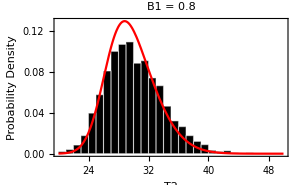
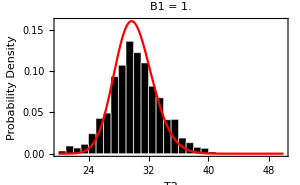
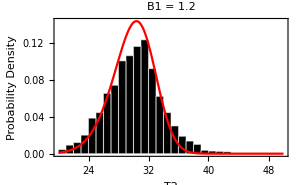

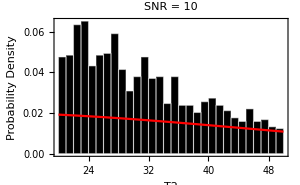
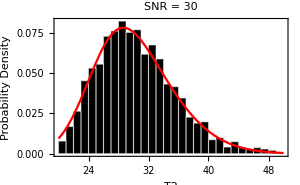
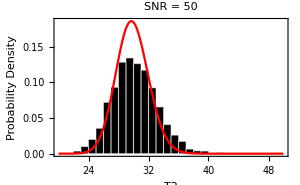

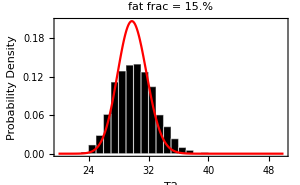
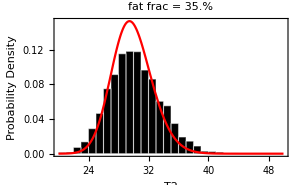

```mathematica
Row@(Hist[T2B1[[#]],{20,50},AxesLabel->"T2",PlotLabel->"B1 = "<>ToString@b1[[#]]]&/@Range[2,Length[b1],4])
Row@(Hist[T2SNR[[#]],{20,50},AxesLabel->"T2",PlotLabel->"SNR = "<>ToString@SNR[[#]]]&/@Range[2,Length[SNR],4])
Row@(Hist[T2Fat[[#]],{20,50},AxesLabel->"T2",PlotLabel->"fat frac = "<>ToString[100fat[[#]]]<>"%"]&/@Range[2,Length[fat],4])
```

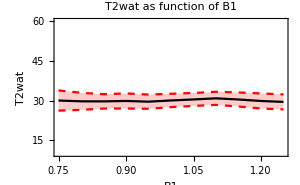
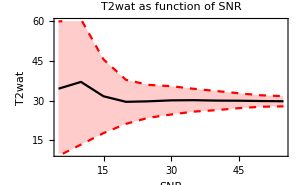
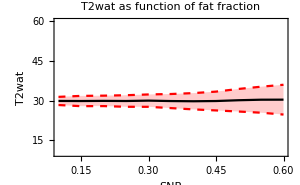

```mathematica
Row[{
ErrorPlot[T2B1,b1,{10,60},AxesLabel->{"B1","T2wat"},PlotLabel->"T2wat as function of B1"],
ErrorPlot[T2SNR,SNR,{10,60},AxesLabel->{"SNR","T2wat"},PlotLabel->"T2wat as function of SNR"],
ErrorPlot[T2Fat,fat,{10,60},AxesLabel->{"SNR","T2wat"},PlotLabel->"T2wat as function of fat fraction"]
}]
```

DTI and IVIM

### Generating diffusion gradients

Generate gradients in the notebook.

```mathematica
grad=GenerateGradients[{6,6,12,24}];
bval={10,100,250,600};
bvals=MapThread[ConstantArray[#1,Length[#2]]&,{bval,grad}];
grads=Flatten[grad,1];
bvals=Flatten[bvals,1];
```

```mathematica
GradientPlot[grads,bvals]
```

-Graphics3D-

```mathematica
ListSpherePlot[bvals grads,SphereSize->30,SphereColor->Blue]
```

-Graphics3D-

Or generate Gradients in the GUI

```mathematica
GenerateGradientsGUI[]
```

### Import The Data

```mathematica
{dwi,grad,val,dwivox}=ImportNiiDiff["DTIdata.nii"];
{datareg,dwivox}=ImportNii["DTIdata-reg.nii"];
tens=Transpose@ImportNii["DTI-tensor.nii",NiiMethod->"data"];
{labels,vox}=ImportNii["labels.nii"];
```

### Prep the IVIM and DTI data

#### Sort and mask

First step is to order and Normalize the diffusion data. Also find all the unique b - values and their positions.

```mathematica
dwi=NormalizeData[dwi];
{dwi,grad,val}=SortDiffusionData[dwi,grad,val];
{bval,pos}=UniqueBvalPosition[val];
bmat = Bmatrix[val,grad];
mdata=Mean@Transpose@dwi;
```

```mathematica
GradientPlot[grad,val]
```

```mathematica
PlotData[mdata,dwivox]
```

```mathematica
mask=Mask[mdata,MaskSmoothing->True,MaskComponents->2,MaskClosing->3];
dwi=MaskData[dwi,mask];
```

```mathematica
PlotData[mdata,mask, dwivox]
```

#### Denoise DWI data

Denoise with a PCA based method, if noise is also measured it can be used as an input.

```mathematica
({dwiN,sigma} = PCADeNoise[dwi,mask,PCAOutput->False,PCATollerance->0];)//AbsoluteTiming
```

```mathematica
PlotData[dwiN,MaskData[dwi-dwiN,mask],dwivox,PlotRange->{{0,150},{-15,15}}]
```

With the sigma map from the PCA denoise the SNR can be calculated.

```mathematica
SNR4D=Transpose[Map[DevideNoZero[#,sigma]&,Transpose[dwiN]]];
```

```mathematica
PlotData[SNR4D,PlotRange->{0,75}]
```

#### Motion and eddy current correction

Register both legs simultaneous.

```mathematica
datareg = RegisterDiffusionData[{dwi,Dilation[mask,2],dwivox},Iterations->100,NumberSamples->1500,DeleteTempDirectory->False];
```

```mathematica
PlotData[dwiN,datareg]
```

Separately register the left and right leg

```mathematica
datareg = RegisterDiffusionDataSplit[{dwiN,Dilation[mask,2],dwivox},Iterations->100,NumberSamples->1500];
```

### IVIM Fitting

#### Whole volume calibrate

Calculate the Iso images from each b - value and calculate the mean signal volume

```mathematica
dwiIso=Transpose[Mean[Transpose[datareg[[All,#]]]]&/@pos];
sig = MeanSignal[datareg];
sigI=MeanSignal[dwiIso];
```

Fit and show the IVIM signal of the whole volume

```mathematica
fiti=IVIMCalc[sig,val,{1,.05,.003,.1}];
fitIi=IVIMCalc[sigI,bval,{1,.05,.003,.1}];

PlotIVIM[fiti,sig,val,ImageSize->200]
PlotIVIM[fitIi,sigI,bval,ImageSize->200]
```

#### IVIM fit

Fit using the whole volume fit as a initial guess and using a fixed D*

```mathematica
{S0Ii,fracI,diff,pDiff}=IVIMCalc[dwiIso,bval,fiti,IVIMConstrained->False,Parallelize->True,MonitorIVIMCalc->True,IVIMFixed->True];
fracI=Clip[fracI,{0,1},{0,1}];
```

```mathematica
PlotData[fracI,diff,PlotRange->{{0,.1},{0,0.002}}]
```

```mathematica
res=IVIMResiduals[dwiIso,bval,{S0Ii,fracI,diff,pDiff}];
```

```mathematica
PlotData[dwiIso,res,PlotRange->{{0,200},{0,10}}]
```

#### Split signals into perfusion and diffusion

With a IVIM fit you can remove the perfusion contribution form the original DWI signal

```mathematica
{dataCor,dataSyn}=IVIMCorrectData[datareg,{S0Ii,fracI,pDiff},val,FilterMaps->False,FilterType->"Laplatian",FilterSize->0.8];
```

```mathematica
PlotData[dataCor,dataSyn,PlotRange->{0,100}]
```

### Tensor analysis

#### Fit the tensors

```mathematica
Column@Options[TensorCalc]
```

MonitorCalc→True
Method→iWLLS
FullOutput→True
RobustFit→True
Parallelize→True
RobustFitParameters→{0.0001,6}

Calculate tensor from corrected data

```mathematica
{tens,S0,outlier,res}=TensorCalc[datareg,grad,val];
```

Convert Tensor To matrix and vector format

```mathematica
tensMat=TensMat[tens];
tensVec=TensVec[tensMat];
Dimensions/@{tensMat,tensVec}
```

{{25,160,160,3,3},{6,25,160,160}}

Plot the tensor.

```mathematica
crp=FindCrop[mdata];
tensPlot=(ApplyCrop[#,crp]&/@tens)/. 0.->-1;
```

```mathematica
PlotData[GridData[Flatten[TensMat[tensPlot],{4,5}],3],PlotRange->{-0.001,0.002}]
```

```mathematica
{ax,cor,sag}=GridData3D[tensPlot,2];
```

```mathematica
PlotData[ax,PlotRange->{-0.001,0.002}]
```

```mathematica
PlotData[sag,PlotRange->{-0.001,0.002}]
```

```mathematica
PlotData[cor,PlotRange->{-0.001,0.002}]
```

Calculate tensor using only high b-values, first find the positions of the high b-values ad then select the correct data and fit the tensor.

```mathematica
selH=Flatten@pos[[Flatten@Position[bval,_?((#≥200)&)]]];
{tensH,S0H,outlierH,resH}=TensorCalc[datareg[[All,selH]],grad[[selH]],val[[selH]],FullOutput->True];
```

```mathematica
PlotData[S0H,Total@Transpose@outlierH]
```

Based on the tensor residuals you can estimate a noise sigma map however this will severely overestimate the sigma

```mathematica
sigmaT=SigmaCalc[datareg[[All,selH]],Join[tensH,{S0H}],grad[[selH]],val[[selH]]];
```

```mathematica
PlotData[S0H,sigmaT]
```

#### Analyse Tensor parameters

ParameterCalc will calculate l1, l2, l3, MD and FA. Internally it uses EignvalCalc, ADCCal and FACalc

```mathematica
par=ParameterCalc[tens];
```

```mathematica
PlotData[par[[4]],par[[5]],PlotRange->{{0,3},{0.1,.5}}]
```

Get the parameters from muscle masks in table form

```mathematica
{masks,labs}=SplitSegmentations[labels];
TableForm@GetMaskMeans[par[[4]],masks,"MD"]
TableForm@GetMaskMeans[par[[5]],masks,"FA"]
```

Plot the parameters prom a muscle mask as a Histogram to evaluate their distribution

```mathematica
Grid@Partition[Hist[GetMaskData[par[[4]],#],Method->"Both"]&/@Transpose[masks][[1;;6]],3]
```

#### Calculate Tensor angles

First filter the tensor using a diffusionFilter and anisotropic smoothing.

```mathematica
tensF=AnisoFilterTensor[tens,datareg];
```

```mathematica
ColorFAPlot[tensF]
```

Calculate the eigenvectors and their angle with respect to the slice normal

```mathematica
eigVal=EigenvecCalc[tensF];
angMap=AngleCalc[eigVal[[All,All,All,1]],{0,0,1},Distribution->"0-90"];
```

```mathematica
PlotData[angMap,PlotRange->{0,90}]
```

Simulate Tensor Data and fit testing

### Simulate Diffusion signal

MRI acquisition parameters used in simulation

```mathematica
grad=Prepend[GenerateGradients[16,VisualOpt->False],{0.,0.,0.}];
bvec=Prepend[ConstantArray[450,Length[grad]-1],0]//N;
{TR,TE}={2990,49};
parMus={0.9,1200,37};(*pd,T1,T2*)
parFat={0.1,300,80};
dim={50,50};(*2500 voxels*)
```

diffusion properties of fat and muscle

```mathematica
eigFat={0.8,0.8,0.8}/1000.;
{MDfat,FAfat}=#[eigFat]&/@{ADCCalc,FACalc};
trueFat=Join[1000*eigFat,{1000MDfat,FAfat}];

eigMus={1.6,1.4,1.0}/1000.;
{MDmus,FAmus}=#[eigMus]&/@{ADCCalc,FACalc};
trueMus=Join[1000*eigMus,{1000MDmus,FAmus}];
```

relative signal of muscle and fat, muscle signal is set to 1 and fat signal is relative to that

```mathematica
sigMus=Signal[parMus,TR,TE];
sigFat=Signal[parFat,TR,TE];
{sigMus,sigFat}=1000{sigMus,sigFat}/sigMus;
```

SNR and fat range for simulation

```mathematica
SNR=Range[5,55,5];
fat=N@Range[0,60,5]/100;
```

Each slice has a different SNR value

```mathematica
diffSNRData=AddNoise[CreateDiffData[sigMus,eigMus,bvec,grad,dim],#,NoiseSize->"SNR"]&/@SNR;
Dimensions[diffSNRData]
```

{11,17,50,50}

Each slice has a different fat concentration and all data has an SNR of 30

```mathematica
diffFatData=((1-#)CreateDiffData[sigMus,eigMus,bvec,grad,dim]+# CreateDiffData[sigFat,eigFat,bvec,grad,dim])&/@fat;
diffFatData=AddNoise[diffFatData,1000/30.];
Dimensions[diffFatData]
```

{13,17,50,50}

### Fit the simulated diffusion signal

```mathematica
{tensSNR,S0SNR,outSNR,resSNR}=TensorCalc[diffSNRData,grad,bvec];
{tensFat,S0Fat,outFat,resFat}=TensorCalc[diffFatData,grad,bvec];
```

$Aborted

$Aborted

Calculate Parameters with and without rejection of negative eigenvalues

```mathematica
parSNR=ParameterCalc[tensSNR,Reject->False];
parFat=ParameterCalc[tensFat,Reject->False];
```

```mathematica
parSNRT=ParameterCalc[tensSNR,Reject->True];
parFatT=ParameterCalc[tensFat,Reject->True];
```

### Evaluate the fits

Show histogram of MD and FA with different SNR values

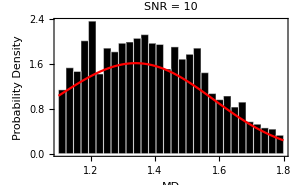
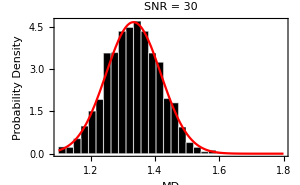
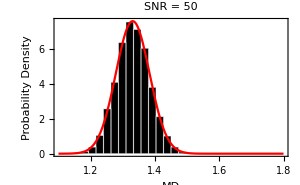

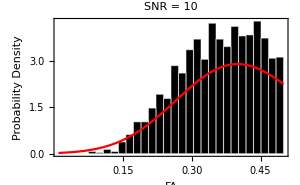
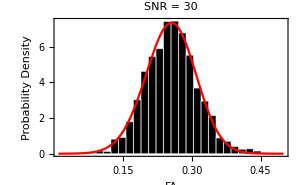
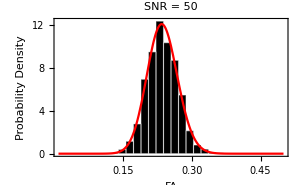

```mathematica
Row@(Hist[parSNR[[4,#]],{1.1,1.8},AxesLabel->"MD",PlotLabel->"SNR = "<>ToString@SNR[[#]]]&/@Range[2,Length[SNR],4])
Row@(Hist[parSNR[[5,#]],{0.01,0.5},AxesLabel->"FA",PlotLabel->"SNR = "<>ToString@SNR[[#]]]&/@Range[2,Length[SNR],4])
```

Show histogram of MD and FA with different fat values

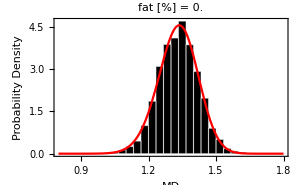
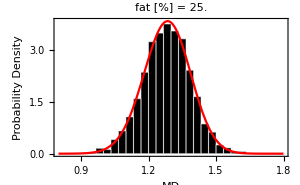
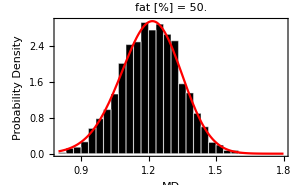

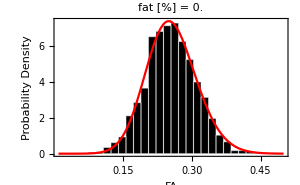
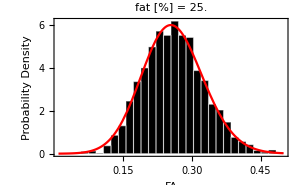
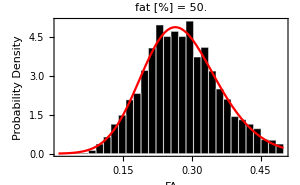

```mathematica
Row@(Hist[parFat[[4,#]],{0.8,1.8},AxesLabel->"MD",PlotLabel->"fat [%] = "<>ToString[100fat[[#]]]]&/@Range[1,Length[fat],5])
Row@(Hist[parFat[[5,#]],{0.01,0.5},AxesLabel->"FA",PlotLabel->"fat [%] = "<>ToString[100fat[[#]]]]&/@Range[1,Length[fat],5])
```

```mathematica
Row[{
ErrorPlot[parSNR[[4]],SNR,{0.8,2},AxesLabel->{"SNR","MD"},PlotLabel->"MD as function of SNR"],
ErrorPlot[parSNR[[5]],SNR,{0.15,0.5},AxesLabel->{"SNR","FA"},PlotLabel->"FA as function of SNR"]
}]
```

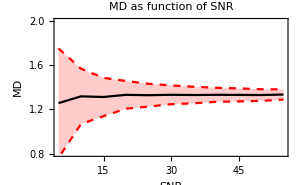
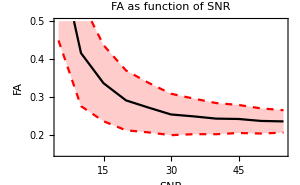

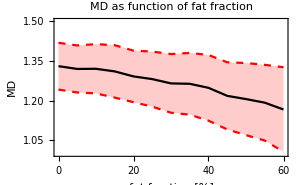
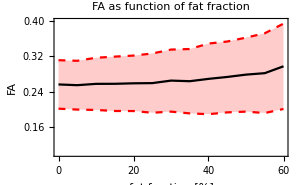

```mathematica
Row[{
ErrorPlot[parFat[[4]],100fat,{1.0,1.5},AxesLabel->{"fat fraction [%]","MD"},PlotLabel->"MD as function of fat fraction"],
ErrorPlot[parFat[[5]],100fat,{0.1,0.4},AxesLabel->{"fat fraction [%]","FA"},PlotLabel->"FA as function of fat fraction"]
}]
```

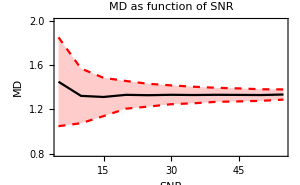
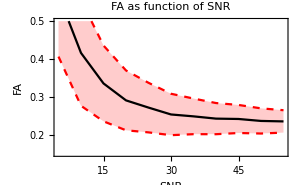

```mathematica
Row[{
ErrorPlot[parSNRT[[4]],SNR,{0.8,2},AxesLabel->{"SNR","MD"},PlotLabel->"MD as function of SNR"],
ErrorPlot[parSNRT[[5]],SNR,{0.15,0.5},AxesLabel->{"SNR","FA"},PlotLabel->"FA as function of SNR"]
}]
```

```mathematica
Row[{
ErrorPlot[parFatT[[4]],100fat,{1.0,1.5},AxesLabel->{"fat fraction [%]","MD"},PlotLabel->"MD as function of fat fraction"],
ErrorPlot[parFatT[[5]],100fat,{0.1,0.4},AxesLabel->{"fat fraction [%]","FA"},PlotLabel->"FA as function of fat fraction"]
}]
```

-Graphics--Graphics-

J-coupling simulations

### Show Fat spin system

Fat contains multiple peak with various j coupling frequencies

```mathematica
sys=GetSpinSystem/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
Total[Flatten[Times@@#&/@sys[[All,{3,5}]]]]
tabs=Column[SysTable[sys]]
```

9 A+84 B+6 C+12 D+6 E+2 G+2 H+I+6 J

fatGly
 | G
4.2
2 | H
4.45
2 | I
5.15
1
    G | - | -12.4 | 7.
    H | - | - | 7.
    I | - | - | -
fatStart
 | B
1.3
6 | C
1.6
6 | E
2.27
6
    B | - | 7.1 | -
    C | - | - | 7.1
    E | - | - | -
fatDouble
 | B
1.3
12 | D
2.03
12 | J
5.3
6
    B | - | 7.1 | -
    D | - | - | 6.2
    J | - | - | -
fatEnd
 | B
1.3
6 | A
0.9
6 | A
0.9
3
    B | - | 8 | -
    A | - | - | -
    A | - | - | -
fatMet
 | B
1.3
60
    B | -

### Glutamate spectra with Steam

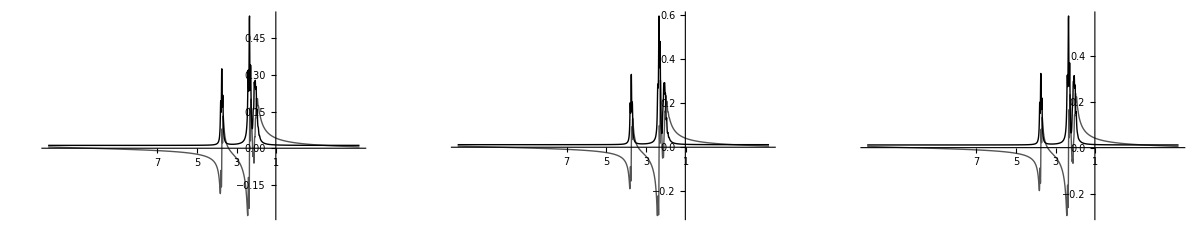

```mathematica
sys=GetSpinSystem["glu"];
{din,struct}=SimHamiltonian[sys];
echoTime=18;

pls=Table[
dout=SequenceSteam[din,struct,{echoTime,tm}/1000];
{time,fids,ppm,spec,dout}=SimReadout[dout,struct,
ReadoutSamples->2048,ReadoutBandwith->2000,Linewidth->5];
pl=PlotSpectrum[ppm,spec,PlotRange->{{1,7},Full}]
,{tm,{6,18,31}(*various mixing times*)}];
GraphicsRow[pls,ImageSize->1200]
```

### Simulate Fat Spectra

#### PulseAcquire

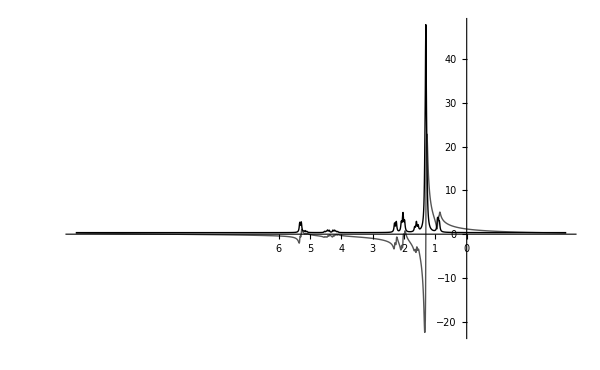

```mathematica
out=Map[(
sys=GetSpinSystem[#];
{din,struct}=SimHamiltonian[sys,FieldStrength->3];
dout=SequencePulseAcquire[din,struct];
SimReadout[dout,struct,
ReadoutSamples->2048,ReadoutBandwith->2000,Linewidth->5]
)&,{"fatGly","fatStart","fatDouble","fatEnd","fatMet"}];
ppm=out[[1,3]];
spec=Total@out[[All,4]];
pl=PlotSpectrum[ppm,spec]
```

#### Spin echo

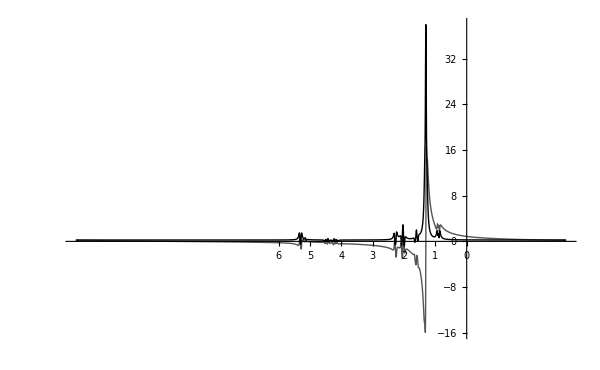

```mathematica
out=(
sys=GetSpinSystem[#];
{din,struct}=SimHamiltonian[sys];
dout=SequenceSpinEcho[din,struct,50/1000];
SimReadout[dout,struct,
ReadoutSamples->2048,ReadoutBandwith->2000,Linewidth->5]
)&/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
ppm=out[[1,3]];
spec=Total@out[[All,4]];
pl=PlotSpectrum[ppm,spec]
```

#### STEAM

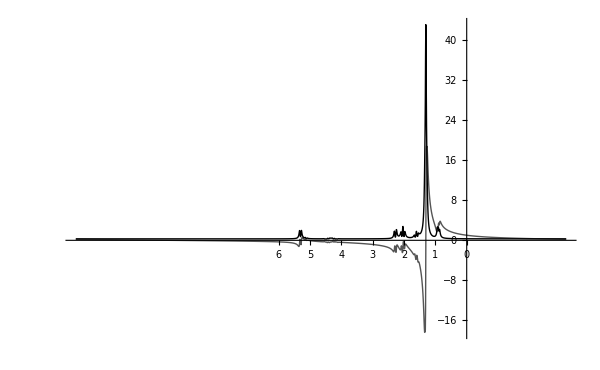

```mathematica
out=(
sys=GetSpinSystem[#];
{din,struct}=SimHamiltonian[sys];
dout=SequenceSteam[din,struct,{50,10}/1000];
SimReadout[dout,struct,
ReadoutSamples->2048,ReadoutBandwith->2000,Linewidth->5]
)&/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
ppm=out[[1,3]];
spec=Total@out[[All,4]];
pl=PlotSpectrum[ppm,spec]
```

### Fat STEAM with various TEs

```mathematica
(*simuluate STEAM j coupling for various TEs*)
TEs=Range[10,100,10];
out=(
{din,struct}=SimHamiltonian[#];
ParallelTable[
dout=SequenceSteam[din,struct,{i,16}/1000];
SimReadout[dout,struct,ReadoutSamples->1024,ReadoutBandwith->2000,Linewidth->10]
,{i,TEs}]
)&/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
ppm=out[[1,All,3]];
spec=Total[out[[All,All,4]]];
```

```mathematica
(*define the T2 relaxation*)
t2sim=90;
T2relax=Exp[-TEs/t2sim];
max=T2relax[[1]]Max[Abs@spec];
pls=MapThread[PlotSpectrum[#1,#2 #3,PlotRange->{{0,7},{-.5,1}}]&,{ppm,spec/max,T2relax}];
```

```mathematica
Manipulate[pls[[n]],{{n,1,"echo time"},1,Length[pls],1},SaveDefinitions->True]
```

Cardiac data processing and simulation

### Simulate Cardiac Shape

```mathematica
pars={{73,2.85,2.8,0.02,0.38},{62.9,3.35,7.9,0.17},106};
```

```mathematica
{mask,vox,pars}=CreateHeart[pars];
```

```mathematica
voxn={6,3,3};
mask=Round@RescaleData[mask,{vox,voxn},InterpolationOrder->2];
vox=voxn;
```

```mathematica
maskR=Round[DataTransformation[mask,vox,{0,10,10},InterpolationOrder->2]];
```

```mathematica
dat=mask RandomVariate[NormalDistribution[50,10],Dimensions[mask]];
```

### Analyse Cardiac shape

```mathematica
{off,vec,inout,pl}=CentralAxes[mask,vox];
{off,vec,inout,pl}=CentralAxes[maskR,vox];
```

Calculate Wall distance map

```mathematica
{wall,der,fit}=CalculateWallMap[maskR,vox,ShowPlot->True];
```

Calculate the myocardial coordinate system.

```mathematica
{{rad,nor,cir},plots}=CardiacCoordinateSystem[maskR,vox,ShowPlot->True];
```

### Cardiac Segmentation

#### perform segmentation

Segment the hart according to the AH17 model and provide the segments as masks and radial sampleling points

```mathematica
{segmask,segang,{points,slices}}=CardiacSegment[dat,mask,off];
```

Plot The masks

```mathematica
PlotSegmentMask[mask,segmask,vox]
```

Plot the radial samples

```mathematica
PlotSegments[mask,dat,segang]
```

#### Analyse data based on segmentation

Use the Radial samples to sample a dataset

```mathematica
MeanStd[GetMaskData[dat,#]]&/@segmask
```

{±±51.109.69,±±50.7010.68,±±49.9010.80,±±52.5011.25,±±49.209.09,±±50.409.40,±±49.809.83,±±49.0010.03,±±50.0010.79,±±49.2010.38,±±51.6010.34,±±50.0011.64,±±49.1010.01,±±49.2010.50,±±50.609.20,±±51.2010.10,±±50.709.84}

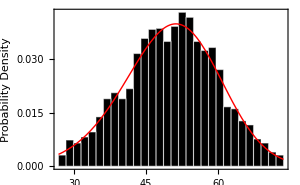

```mathematica
Hist[GetMaskData[dat,mask]]
```

```mathematica
TableForm@GetMaskMeans[dat,Transpose[segmask],"noise"]
```

noise mean | noise std | noise Median | noise 5% | noise 95%
51.7153 | 9.32549 | 50.9065 | 37.8221 | 68.3542
49.0624 | 9.98713 | 49.0027 | 32.7388 | 65.5899
49.385 | 9.50268 | 50.1002 | 32.5891 | 63.7409
53.3447 | 9.39639 | 53.9135 | 36.9489 | 67.7904
49.3594 | 7.86485 | 50.2708 | 35.0179 | 60.6484
50.4064 | 9.76957 | 49.7963 | 35.4206 | 67.4826
49.919 | 9.34198 | 50.1838 | 34.1088 | 64.8189
49.1963 | 9.50878 | 49.1979 | 33.5532 | 64.8343
50.4499 | 7.56188 | 51.7085 | 36.2105 | 60.5001
48.8443 | 9.95563 | 48.8738 | 32.4191 | 65.1687
52.0305 | 10.1099 | 52.6391 | 34.3949 | 67.5791
51.3802 | 12.0003 | 51.5754 | 31.3143 | 70.7769
48.8101 | 10.8451 | 48.9902 | 30.6696 | 66.333
48.6804 | 9.52328 | 48.5696 | 33.2097 | 64.5306
50.9902 | 9.19986 | 50.9613 | 35.908 | 66.1713
51.0468 | 10.5616 | 51.5962 | 32.7607 | 67.4452
51.5071 | 8.97184 | 50.6755 | 38.2393 | 67.5905

Perform Radial sampling of data based on the segmentation

```mathematica
{pts,radSamp}=RadialSample[mask,dat,segang];
```

#### Visualize results

Visualisation can be done using Busleyeplots or transmural profiles

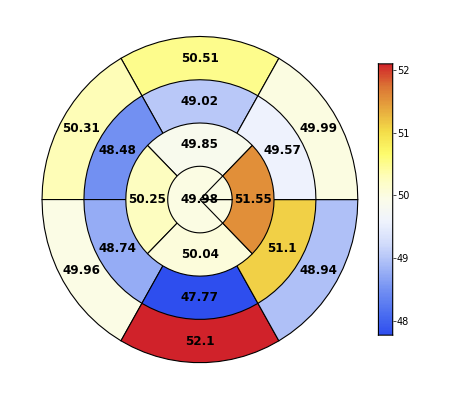

```mathematica
radSampF=Flatten/@radSamp;
BullseyePlot[radSampF,BullPlotMethod->"Static",ImageSize->400]
```

```mathematica
BullseyePlot[radSampF,ImageSize->300]
```

Make a trans mural plot of the data for segment 5

```mathematica
TransmuralPlot[Flatten[radSamp[[5]],1]]
```

Make a trans mural plot of the wall distance map

```mathematica
{wall,der}=CalculateWallMap[mask,vox,ShowFit->False,MaskWallMap->True];
```

```mathematica
{pts,wallSamp}=RadialSample[mask,100wall,segang];
```

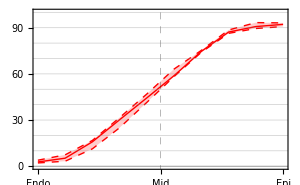

```mathematica
TransmuralPlot[Flatten[wallSamp[[3]],1],PlotRange->{0,100}]
```